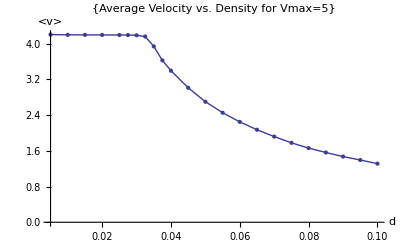

```mathematica
vbar5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax5.txt",{Number,Number}];
a=ListPlot[vbar5,PlotLabel->{"Average Velocity vs. Density for Vmax=5"},AxesLabel->{d,"<v>"},PlotRange->Full];
b=ListLinePlot[vbar5,PlotLabel->{"Average Velocity vs. Density for Vmax=5"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a,b]
```

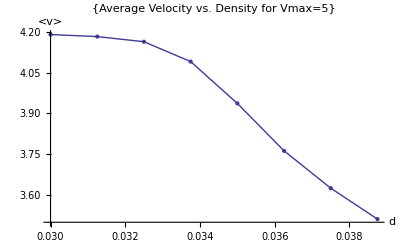

```mathematica
vbar52=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax5.fine.txt",{Number,Number}];
a2=ListPlot[vbar52,PlotLabel->{"Average Velocity vs. Density for Vmax=5"},AxesLabel->{d,"<v>"},PlotRange->Full];
b2=ListLinePlot[vbar52,PlotLabel->{"Average Velocity vs. Density for Vmax=5"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a2,b2]
```

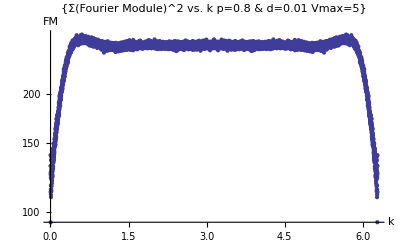

```mathematica
lsqdsum080125v5=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/fourier.1d.averaged.d0.0325.p0.8.u.check.v5.uniform.txt",{Number,Number}];
ListLogPlot[lsqdsum080125v5,PlotLabel->{"Σ(Fourier Module)^2 vs. k  p=0.8 & d=0.01 Vmax=5"},AxesLabel->{k,FM},PlotRange->Full]
```

```mathematica
vbar5
```

{{0.005,4.20465},{0.01,4.1978},{0.015,4.19716},{0.02,4.19615},{0.025,4.19444},{0.0275,4.19324},{0.03,4.18793},{0.0325,4.16038},{0.035,3.93928},{0.0375,3.62602},{0.04,3.39454},{0.045,3.01242},{0.05,2.69986},{0.055,2.45347},{0.06,2.24807},{0.065,2.07208},{0.07,1.91903},{0.075,1.77935},{0.08,1.66079},{0.085,1.56275},{0.09,1.47156},{0.095,1.3941},{0.1,1.31258}}

```mathematica
vbar52
```

{{0.03,4.18997},{0.03125,4.18247},{0.0325,4.16359},{0.03375,4.09055},{0.035,3.93686},{0.03625,3.76246},{0.0375,3.62531},{0.03875,3.51154}}